# Лабораторная работа №3 Вариант №13

Выполнил студент группы 0В92
Толстихин Илья

Импортируем котировки согласно 13 варианту (4, 9, 10, 11, 12, 13, 17)

```mathematica
X=Flatten[Import["D:\\Doc\\tpu\\многомерные статистические методы\\Cot1.xlsx"],1]
```

{{0.0124444,-0.0297653,-0.00835322,-0.0132159,-0.0464768,-0.0455172,-0.0465423},{-0.0112511,-0.0564202,-0.0366864,-0.0434783,-0.0124164,-0.0224274,-0.0132159},{0.0311526,-0.0260458,-0.0388128,-0.00378788,0.00943396,-0.043871,0.0163561},{0.0272546,0.0102564,0.0043956,0.00377358,0.0285714,0.039555,0.00926121},{0.047694,-0.0595855,0.00331126,0.0530303,-0.0151961,0.015444,-0.0397281},{0.00661157,-0.0278729,-0.0199336,-0.01,0.0111057,-0.0156863,-0.0173682},{-0.0437604,-0.0299715,-0.0423453,-0.0348515,-0.0205078,-0.00643501,0.029524},{-0.0396939,0.00323326,-0.0125,-0.00574053,-0.0296651,-0.0127877,-0.0140728},{0.0185526,0.00370714,0.0216049,-0.0197869,-0.0130112,-0.00631313,0.00612245},{0.0298391,0.00395349,-0.0136698,-0.0160448,-0.0266055,0.00627353,0.0246407},{-0.0225443,-0.0410927,0.00414938,-0.180683,-0.000893655,-0.00883838,-0.0324211},{-0.00188976,-0.0181655,-0.0760417,-0.105754,0.000892857,0.,-0.0679038},{-0.0028293,-0.00440529,0.0203291,0.0323488,0.0437891,0.,0.022341},{0.0188088,0.060307,-0.0227273,0.0491279,0.017757,0.0237797,0.015625},{-0.0166134,-0.00606768,0.0231884,-0.030266,0.0104662,0.,-0.00297619},{-0.0556254,0.00719091,0.0514342,0.00326409,-0.0144231,-0.0153846,0.0346192},{0.0101221,-0.0259346,0.0250261,-0.289074,0.,-0.00883838,0.0155738},{-0.0366917,0.00774311,0.0374332,-0.0357968,0.00521327,-0.00500626,0.0424646},{0.0287206,-0.0433785,-0.00444444,0.11728,0.0028585,-0.0249066,-0.026087},{-0.0110514,-0.025297,-0.0176991,0.0123769,-0.00716675,0.0133657,-0.021822},{0.0119645,0.00450547,-0.023913,-0.0457801,0.00189753,0.00492611,0.00787891},{-0.0145014,-0.0150862,-0.0562633,-0.0584495,-0.00855513,0.00866337,-0.0453501},{-0.00589449,-0.0225053,-0.0904523,0.0298059,0.000942507,-0.00873908,-0.0439824},{0.00380897,0.000830565,0.0230415,-0.0240533,-0.00849057,-0.0136139,-0.0101494},{-0.00308824,0.0438487,0.0264151,-0.00651163,0.00561272,0.003663,0.014218},{-0.0123149,-0.0343404,0.0116279,-0.000693161,-0.0686736,-0.393382,-0.0209615},{0.000724113,-0.0546333,-0.00490196,-0.039021,0.03125,-0.176781,-0.0161989},{-0.0057971,-0.0255031,-0.0526829,-0.00977778,-0.0104498,0.0792227,-0.00797034},{0.0309798,0.0196231,0.0352178,0.0264085,-0.0341727,-0.00162338,0.0353071},{0.00237918,0.00118906,0.00864553,-0.0533454,0.0169565,0.0307942,0.00362181},{0.00372634,0.00654762,-0.0271318,-0.0266094,0.0106148,-0.0819398,-0.00918309},{-0.00179533,-0.0265628,0.0188679,-0.156982,0.00759946,0.0401855,-0.00322275},{0.00537634,0.0175097,0.0192308,0.00451671,0.0126126,-0.111111,0.0209751},{0.0313814,0.00871287,-0.0137255,-0.125045,-0.00364964,-0.0166667,-0.000386026},{-0.0339482,0.00679185,0.0183752,-0.177609,-0.00454545,0.0135424,0.0223809},{-0.0509745,-0.0197104,0.00985222,-0.144932,-0.00588235,-0.015896,0.0146043},{0.0299572,0.0177515,-0.00895522,0.0156736,0.00134953,0.00426743,-0.00881234},{-0.00147059,0.00582329,-0.0364892,-0.00887322,-0.018018,-0.00285714,-0.0168751},{-0.0207048,-0.039184,0.00951475,-0.00951807,-0.00707965,0.022792,-0.0191332},{0.0217235,0.0204082,0.0230548,-0.0675498,0.00307557,-0.0327988,0.0178161},{0.0235294,0.0178571,0.027532,-0.0452767,-0.00352578,-0.0303458,0.000585138},{0.0253012,0.0121212,0.0121335,0.17123,0.0114185,0.00753425,0.0267369},{0.0327565,0.0408998,-0.0102354,0.0961414,0.00799645,0.0752243,0.0274714},{-0.0108626,0.0021322,0.0466059,-0.256425,-0.00134348,0.000746269,0.00618557},{-0.0192794,0.00705128,0.0201913,0.00829545,-0.00670841,0.00970874,0.0211618},{0.0182946,0.0088229,0.0021692,0.054658,0.00844069,0.086727,0.0214074},{0.0192672,0.0330004,0.0369565,0.105697,0.0456989,0.0272502,-0.00931341},{0.0177134,0.0103278,0.020316,0.0149092,0.0610329,0.,0.0128755},{-0.0229508,-0.0313067,-0.0264977,-0.0731976,0.002,-0.0118846,-0.00869565},{0.00160256,0.00131984,0.0381594,-0.0262821,-0.0470942,0.00251678,0.0366379},{-0.0176565,-0.0526432,-0.042007,0.118801,0.00239234,0.00841043,-0.0134228},{0.0264984,0.000836995,-0.0167973,-0.0228239,0.0330935,0.0212044,0.0401766},{-0.0207388,-0.0303665,0.00330396,-0.000554401,-0.00496032,0.,0.0124195},{0.0031746,-0.0148374,-0.00110497,0.0261809,0.0113524,-0.00433276,-0.00209595},{0.0350318,0.0276387,0.00993377,0.0677098,-0.000499251,0.050906,0.0285847},{0.0181518,-0.00102987,-0.00668896,0.0828502,-0.0638723,0.02,0.00358852},{-0.0087395,-0.0135802,-0.0321152,-0.255199,0.0356473,-0.0463822,-0.0372149},{0.000333222,-0.00284206,0.0182403,0.0152419,0.0111868,0.00620567,0.},{-0.0065,-0.0157895,-0.042623,0.0417227,-0.0113133,-0.015165,-0.0423611},{-0.0216923,0.00358709,-0.0167715,-0.00842697,0.016537,-0.0685413,-0.0375305},{0.0012966,0.0056,0.0123711,0.0387187,-0.00197824,-0.00328947,-0.0196918},{-0.0110354,-0.0213194,-0.00313152,-0.020284,-0.00345508,-0.0459016,-0.00335852},{0.0346709,-0.00433241,-0.0322581,0.00781028,-0.0108214,0.0242947,0.00753138},{0.0023279,0.00784314,0.0322581,-0.0237584,0.0053528,0.0273092,0.00801012},{0.0201667,0.00395257,0.0333333,0.0514469,-0.00293542,-0.014038,0.0108372},{0.00153087,0.015873,0.0161638,0.0129698,-0.0097561,0.0325733,0.00408163},{-0.00562181,-0.0205645,-0.00766703,0.0338958,-0.0236715,-0.0193603,-0.0293356},{0.0191428,-0.0015804,0.00543478,-0.00463679,0.0136857,0.00990917,0.0299665},{-0.00621762,-0.0374753,-0.0153005,-0.0212308,-0.0430622,-0.0166806,-0.0384532},{-0.0111569,-0.0026616,-0.0118407,0.0260621,-0.0279817,-0.0164069,-0.0255877},{0.0145985,0.0254077,0.0234043,0.0256767,-0.0200803,0.0258273,-0.0239351},{0.000861326,0.0159533,-0.00326797,-0.0139705,-0.0279965,0.003314,-0.00435816},{-0.00862069,-0.0088968,-0.0162866,-0.0200407,-0.0382979,-0.0399002,-0.0321499},{0.00615385,0.010778,0.0235043,0.0191865,-0.0786885,0.0135891,0.0347793},{0.0213278,-0.00336767,0.0306346,0.0359937,0.0345745,0.0372771,0.0108889},{-0.0516696,-0.00750247,0.00112867,-0.0543831,-0.042503,-0.0176768,0.00140112},{-0.00116979,-0.010386,0.0169492,0.00384911,-0.0570026,0.00744417,0.00501102},{-0.0373894,-0.0124127,-0.0103448,0.0106646,-0.0725,0.0116667,0.0020145},{-0.0152856,0.0114943,0.0102389,-0.0301515,-0.00899101,-0.00084317,-0.00726686},{-0.0380349,-0.0271318,-0.00804598,0.0248711,-0.019802,-0.00336984,0.01002},{-0.0465649,-0.00849057,-0.0022805,-0.0139969,-0.0275081,-0.0201511,-0.01417},{0.00350109,0.0175865,0.0102389,0.00843558,-0.0141732,0.00740741,0.0207585},{0.0115649,0.00971244,0.0137931,0.0137664,-0.034472,0.0107794,0.00122299},{0.000296209,-0.0186538,-0.0174825,0.00423463,-0.0153107,-0.00419111,-0.0259184},{0.0152593,-0.0054748,0.0091638,0.015593,0.059728,-0.00918197,0.},{0.00707086,-0.0176493,0.0312139,0.01936,-0.00974843,0.00992556,0.00258604},{0.0128788,0.00848708,0.00238663,-0.0128895,0.0127686,0.00835422,0.000997208},{-0.0503454,-0.00130257,-0.0131579,-0.00306057,-0.00946372,0.,-0.0063885},{-0.0375566,0.00520349,0.0141677,0.0223221,-0.0084375,0.00252738,0.00416584},{-0.0143662,0.0285821,0.00479042,0.0289093,-0.00495817,0.0118243,0.0129482},{0.000277701,0.0282692,0.0120337,-0.0926928,-0.00955905,-0.0017094,0.00161453},{-0.0426389,0.00653077,-0.0146163,0.0185759,0.0152718,-0.0059727,-0.0280978},{-0.0359664,-0.0059761,-0.00240096,0.0182965,0.,-0.00339271,-0.00747149},{-0.0222451,-0.00594059,0.0011976,-0.00449871,0.00279156,0.000845309,0.010929},{-0.0251572,0.0181102,0.0059952,-0.00767754,0.000622084,0.00338409,-0.0175612},{-0.0134969,0.0196472,0.00241255,0.0146032,0.00311236,-0.0101868,-0.0168703},{0.0254237,-0.00961145,-0.00362757,-0.0172358,0.00624415,-0.00840336,-0.00781846},{0.00310559,0.0155965,0.0228916,-0.0332542,0.0103676,0.00833333,0.0113529},{-0.00124611,0.00658436,-0.00739827,-0.0222222,0.00507937,-0.00672269,-0.00497608},{0.00174238,-0.0161558,-0.00979192,-0.0164918,0.0331844,-0.000834725,-0.0213293},{-0.0104725,0.0173257,-0.00484848,0.0162242,0.00330033,0.0175146,-0.00578035},{0.,0.0064302,0.0108565,-0.0017991,0.0178808,0.00848896,0.00222469},{-0.000246761,0.000835073,-0.00243902,-0.0625561,0.00505732,-0.0231164,-0.00687477},{-0.0102381,-0.00919348,0.00243309,-0.0160563,-0.0233819,0.0041841,0.00129175},{0.0018315,0.,0.00853659,0.00679235,-0.0198675,-0.00336134,-0.0112712},{0.0150459,0.010352,0.0295203,0.00488486,-0.0649351,-0.00251256,0.00621232},{0.00149031,0.00313808,0.0228137,-0.000420757,-0.0439024,0.015873,0.000735429},{0.000124378,-0.0140609,0.00518807,0.0164026,-0.0505257,0.0135823,-0.0136155},{0.00485135,-0.00496689,-0.011734,0.000427594,-0.00333611,-0.0060241,0.00726085},{-0.000125,0.0111203,0.00773196,0.00199629,-0.000277085,0.00855432,0.00347413},{0.00137483,-0.0141608,-0.0207792,-0.0215745,-0.00387812,0.00172563,0.00917431},{-0.00150188,-0.00616016,-0.0127226,-0.00699301,0.00331126,0.00345722,-0.0131481},{0.00637341,-0.0330612,-0.00125628,-0.0116667,0.000830565,-0.00260191,0.00127947},{0.0140863,0.0102726,-0.00125471,0.0334981,0.00221668,0.00951557,0.00347731},{0.0062508,0.00858283,0.0175439,0.0349432,-0.0019439,0.000873362,0.00514233},{-0.0012837,0.00926112,-0.00382653,0.00426847,0.00221729,0.0297203,0.019568},{0.,-0.0111766,0.0139771,-0.0224686,0.00277778,-0.0045045,-0.0289964},{-0.00153846,0.0223071,0.00902062,-0.012144,-0.00362117,0.00807175,-0.00622141},{-0.0112647,0.00061665,-0.0117035,-0.00085702,0.050791,0.000904159,-0.0141844},{0.0229114,-0.00329083,-0.00128535,-0.0218353,0.,0.,-0.00519993},{-0.00349786,-0.00799508,0.0102696,-0.0114525,-0.0116959,-0.0289593,0.0189083},{0.020914,0.00772829,0.0181582,0.0263739,0.0231214,0.0290237,-0.00181818},{0.0176688,0.0897725,-0.001321,0.0136151,-0.0118343,0.00543478,-0.0119782},{-0.00134228,0.0182391,0.00395778,0.0294752,0.00233918,0.00637523,-0.00322812},{0.0171582,0.0105505,-0.0251656,0.0642963,-0.0196366,0.0320807,-0.00321773},{0.00422804,-0.0180807,0.00258398,-0.0172578,-0.0267318,0.00568182,-0.00623664},{-0.0299959,-0.00295993,-0.0220207,-0.0121401,-0.00839866,0.0133333,-0.00141668},{0.00864362,-0.00862656,0.00633714,0.0036906,0.00999445,-0.00868726,-0.0167993},{-0.00536553,0.0108035,0.00892857,0.00601945,-0.0213124,0.00669856,-0.00469565},{0.000667111,0.00705347,-0.010296,-0.00916149,-0.00164745,-0.00578035,-0.0012117},{0.00881175,-0.0160403,0.,-0.0340052,0.00767544,-0.0258621,0.00121024},{0.00309806,0.00811908,-0.0433121,0.0016369,-0.0110497,-0.00186741,0.00519301},{0.0158087,0.0140973,0.002442,-0.00149054,0.0125683,0.0186393,0.00817818},{-0.00562878,0.00853321,0.00979192,0.000297663,-0.00193691,-0.00949668,0.0101754},{0.000273038,0.0146546,0.,0.0189073,0.,0.0028222,-0.00939383},{0.00655469,-0.0174693,0.0271941,0.0159332,0.013256,0.0245283,0.00491659},{0.0116838,0.0208817,0.0139771,0.0444102,0.00531766,0.0106383,0.0127051},{-0.00556328,0.0158768,0.0360825,0.0450218,-0.0149128,0.0127077,-0.0142985},{0.000691563,-0.0199856,0.0307487,-0.00473133,-0.00221791,-0.0039604,-0.0167401},{-0.000553633,-0.0247875,-0.0151724,-0.0174908,0.00138313,0.00986193,-0.00207972},{0.00456495,-0.00898411,-0.0298913,-0.00694215,0.,0.,0.00553442},{-0.000555864,-0.0269406,-0.00923483,-0.00180565,0.00277008,-0.0159363,-0.0278261},{0.,0.0104491,-0.00653595,-0.00671801,0.,0.00196078,0.00524535},{0.0138889,0.00134801,-0.0194805,0.00227865,-0.00833333,-0.00589391,-0.0170097},{0.,-0.0218223,-0.0089172,-0.0104405,-0.0110193,0.00390625,0.0143837},{0.00661972,-0.00220167,-0.0151515,0.0159832,-0.0217984,0.000980392,-0.00678771},{-0.00396994,-0.00900703,-0.0323383,-0.000820345,-0.0986667,0.,-0.00792179},{0.00522525,-0.00587851,0.0060241,-0.00278689,-0.106796,-0.0225711,0.00100334},{-0.000851789,-0.00411255,0.0218182,0.00653915,0.0350877,0.00287908,0.00820221},{0.00368794,0.00840698,0.00495663,0.00625309,-0.104545,0.00481232,-0.00843882},{-0.00427107,0.00217391,-0.00747198,-0.00546448,0.0288066,0.00193424,0.00619247},{0.00170116,0.0122004,-0.00865266,0.00197628,-0.00211864,0.00193798,0.00522061},{0.000994036,-0.0149978,0.0171569,0.0232673,0.0443975,0.00485437,0.0106653},{0.0098081,0.00347675,-0.0174564,0.00827843,0.0265487,0.0156098,0.000684463},{0.0047373,0.00588748,0.00735294,0.0321976,-0.0477273,0.00099108,0.0210616},{-0.00100966,-0.0177671,-0.0185185,0.0149622,0.0238612,-0.00595238,-0.0250131},{0.0100865,0.0142241,0.0133333,0.0359185,-0.0288889,0.00788955,0.0375427},{0.0317322,0.0216441,0.00982801,0.0509731,0.0431965,0.0347913,-0.00567376},{-0.0523151,-0.00424581,-0.00372208,-0.111328,-0.00677201,-0.0030896,0.012165},{0.00285714,0.0164664,0.00247219,-0.00808436,0.,-0.0102669,-0.0373014},{-0.000716332,-0.0282805,0.00743494,-0.0685146,-0.0224215,-0.00609756,-0.0314866},{0.00286328,-0.00726073,-0.0212235,-0.0505792,-0.0394737,-0.0020202,-0.02402},{0.00933238,0.000218436,0.00488998,-0.0621214,0.,0.00604839,-0.0311126},{0.0249275,0.00568058,0.0110565,-0.0021933,-0.0400844,-0.0020284,0.0363349},{0.00490488,-0.00197759,-0.00124224,-0.00423111,-0.0141988,-0.00101215,0.00655738}}

```mathematica
Covariance[Standardize[X]]
```

{{1.,0.213771,0.0759166,0.26985,0.136202,0.151212,0.109374},{0.213771,1.,0.30446,0.197906,0.0774506,0.273232,0.354995},{0.0759166,0.30446,1.,-0.00208158,0.018267,0.0265199,0.437462},{0.26985,0.197906,-0.00208158,1.,-0.0230132,0.144517,0.0907924},{0.136202,0.0774506,0.018267,-0.0230132,1.,0.134259,0.0240571},{0.151212,0.273232,0.0265199,0.144517,0.134259,1.,0.210165},{0.109374,0.354995,0.437462,0.0907924,0.0240571,0.210165,1.}}

Проверим на независимость:

Уровень значимости принятия гипотезы о независимости факторов очень мал, поэтому факторы зависимы.

```mathematica
Variance[X]
```

{0.000376061,0.000418047,0.000480465,0.00339377,0.000742115,0.00165731,0.000377527}

```mathematica
Covariance[X]; MatrixForm[%]
```

(1. | 0.213771 | 0.0759166 | 0.26985 | 0.136202 | 0.151212 | 0.109374
0.213771 | 1. | 0.30446 | 0.197906 | 0.0774506 | 0.273232 | 0.354995
0.0759166 | 0.30446 | 1. | -0.00208158 | 0.018267 | 0.0265199 | 0.437462
0.26985 | 0.197906 | -0.00208158 | 1. | -0.0230132 | 0.144517 | 0.0907924
0.136202 | 0.0774506 | 0.018267 | -0.0230132 | 1. | 0.134259 | 0.0240571
0.151212 | 0.273232 | 0.0265199 | 0.144517 | 0.134259 | 1. | 0.210165
0.109374 | 0.354995 | 0.437462 | 0.0907924 | 0.0240571 | 0.210165 | 1.)

```mathematica
X0=Standardize[X];
```

```mathematica
A=Covariance[X0];
MatrixForm[%]
k=7;
```

(1. | 0.213771 | 0.0759166 | 0.26985 | 0.136202 | 0.151212 | 0.109374
0.213771 | 1. | 0.30446 | 0.197906 | 0.0774506 | 0.273232 | 0.354995
0.0759166 | 0.30446 | 1. | -0.00208158 | 0.018267 | 0.0265199 | 0.437462
0.26985 | 0.197906 | -0.00208158 | 1. | -0.0230132 | 0.144517 | 0.0907924
0.136202 | 0.0774506 | 0.018267 | -0.0230132 | 1. | 0.134259 | 0.0240571
0.151212 | 0.273232 | 0.0265199 | 0.144517 | 0.134259 | 1. | 0.210165
0.109374 | 0.354995 | 0.437462 | 0.0907924 | 0.0240571 | 0.210165 | 1.)

```mathematica
DS=Tr[A]
```

7.

Получим собственные значения и вектора

```mathematica
La=Eigenvalues[A]
```

{2.02276,1.24674,1.03417,0.878406,0.678611,0.622333,0.516989}

```mathematica
Va=Eigenvectors[A]; TableForm[Va]
```

-0.334782 | -0.517321 | -0.398356 | -0.277958 | -0.142822 | -0.356119 | -0.486963
-0.456679 | 0.0431992 | 0.53376 | -0.466106 | -0.267567 | -0.273203 | 0.375755
-0.0946793 | -0.0319861 | 0.000261477 | -0.523371 | 0.813188 | 0.233836 | -0.0119097
-0.498868 | 0.114307 | -0.308989 | -0.0623841 | -0.304507 | 0.736405 | 0.0606791
0.643156 | -0.0661404 | -0.0352033 | -0.615762 | -0.388357 | 0.221727 | -0.039873
-0.0765198 | 0.83082 | -0.117443 | -0.189473 | -0.0398433 | -0.225597 | -0.449119
0.045032 | 0.147601 | -0.667762 | -0.112307 | 0.0400293 | -0.318607 | 0.643859

```mathematica
Table[La[[i]]/DS,{i,1,k}]
```

{0.288965,0.178105,0.147738,0.125487,0.0969444,0.0889047,0.0738556}

```mathematica
Table[Sum[La[[i]]/DS,{i,1,j}],{j,1,k}]
```

{0.288965,0.467071,0.614809,0.740295,0.83724,0.926144,1.}

Можно сделать вывод о том, что первые 3 компоненты составляют большую часть дисперсии. Целесообразно оставить только их, но, как было сказано выше, по критерию Кайзера следует оставить только 3 компоненты

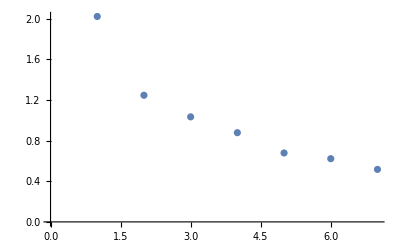

```mathematica
ListPlot[La]
```

По критерию каменистой осыпи можно сделать вывод, что стоит оставить 2 компоненты, так как дальше график не так быстро убывает

Факторные нагрузки

```mathematica
b={Va[[1]]/Sqrt[La[[1]]],Va[[2]]/Sqrt[La[[2]]],Va[[3]]/Sqrt[La[[3]]],Va[[4]]/Sqrt[La[[4]]],Va[[5]]/Sqrt[La[[5]]],Va[[6]]/Sqrt[La[[6]]],Va[[7]]/Sqrt[La[[7]]]};
```

```mathematica
bT=Transpose[b];
X0T=Transpose[X0];
```

Обобщенные факторы

```mathematica
X0.bT // MatrixForm;
```

Тогда оценка значений обобщенных факторов :

```mathematica
{{Subscript[β, 1]=-0.335 Subscript[e, 1], -0.517 Subscript[e, 2], -0.398 Subscript[e, 3], -0.2779 Subscript[e, 4], -0.1428 Subscript[e, 5], -0.356 Subscript[e, 6], -0.4869 Subscript[e, 7]}, {Subscript[β, 2]=-0.456 Subscript[e, 1], +0.043 Subscript[e, 2], +0.533 Subscript[e, 3], -0.466 Subscript[e, 4], -0.267 Subscript[e, 5], -0.273 Subscript[e, 6], +0.375 Subscript[e, 7]}}
```

Относительный вклад признака в дисперсию главной компоненты характеризует квадрат соответствующей координаты вектора.

```mathematica
Va[[1]]^2
```

{0.112079,0.267621,0.158688,0.0772606,0.0203981,0.126821,0.237133}

Вносит вклад первый, второй, третий, шестой, седьмой признаки

```mathematica
Va[[2]]^2
```

{0.208556,0.00186617,0.2849,0.217255,0.071592,0.07464,0.141192}

Вносит вклад первый, третий, четвертый, седьмой признаки

Оценка информативности каждого фактора :

Для первой компоненты : 0.86
Для второй компоненты : 0.85

```mathematica
AL={Va[[1]],Va[[2]]}
```

{{-0.334782,-0.517321,-0.398356,-0.277958,-0.142822,-0.356119,-0.486963},{-0.456679,0.0431992,0.53376,-0.466106,-0.267567,-0.273203,0.375755}}

```mathematica
Ar:=Table[Arrow[{{0,0},{AL[[1,i]],AL[[2,i]]}}],{i,1,k}]
```

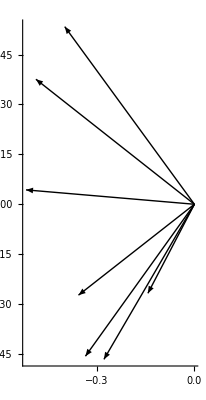

```mathematica
Graphics[Ar, Axes-> True]
```

```mathematica
{{"","ξ1","ξ2","ξ3","ξ4","ξ5","ξ6","ξ7"},Join[{"f1"},AL[[1]]^2/Norm[AL[[1]]]^2],Join[{"f2"},AL[[2]]^2/Norm[AL[[2]]]^2]};MatrixForm[%]
```

( | ξ1 | ξ2 | ξ3 | ξ4 | ξ5 | ξ6 | ξ7
f_1 | 0.112079 | 0.267621 | 0.158688 | 0.0772606 | 0.0203981 | 0.126821 | 0.237133
f_2 | 0.208556 | 0.00186617 | 0.2849 | 0.217255 | 0.071592 | 0.07464 | 0.141192)

```mathematica
Maximize[Total[(Variance[Transpose[AL^2].RotationMatrix[θ]])^4],θ]
```

{1.70773×10^-8,{θ→-1.0458}}

```mathematica
θ=-1.045796479044468;
```

```mathematica
AL1=Transpose[Transpose[AL].RotationMatrix[θ]]
```

{{0.227378,-0.296669,-0.661537,0.264017,0.159948,0.0579179,-0.569222},{-0.518588,-0.425999,-0.0771797,-0.474142,-0.257695,-0.445091,-0.233048}}

```mathematica
Ar1:=Table[Arrow[{{0,0},{AL1[[1,i]],AL1[[2,i]]}}],{i,1,k}]
```

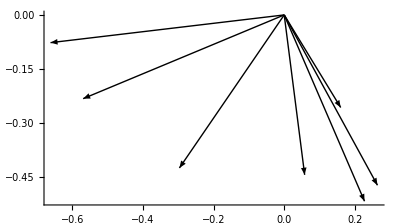

```mathematica
Graphics[Ar1, Axes -> True]
```

```mathematica
{{"","ξ_1","ξ_2","ξ_3","ξ_4","ξ_5","ξ_6","ξ_7"},Join[{"f_1"},AL1[[1]]^2/Norm[AL1[[1]]]^2],Join[{"f_2"},AL1[[2]]^2/Norm[AL1[[2]]]^2]};MatrixForm[%]
```

( | ξ_1 | ξ_2 | ξ_3 | ξ_4 | ξ_5 | ξ_6 | ξ_7
f_1 | 0.051701 | 0.0880127 | 0.437631 | 0.0697047 | 0.0255833 | 0.00335448 | 0.324013
f_2 | 0.268934 | 0.181475 | 0.00595671 | 0.224811 | 0.0664068 | 0.198106 | 0.0543112)